```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
solverRewrite={"SOLVER",{"GPAT"->"AT","GP"->"G","NEAT"->"N"}};
functionImplRewrite={"GPAT.FUNCTION_IMPL",{"gpat.ATFunctions$"->"N","gpat.ATFunctionsNoConsts$"->"NC","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L"}};
distanceRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
plotRange={All,{0,100}};
listOfDirectProblems={"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"};
listOfIndirectProblems={"Bit Reverse","Bit Shift","Bit Rotate","Visual Discrimination","Parity"};
```

## Normal Experiments All Comparison [TEMPLATE]

```mathematica
names={"NEAT_GECCO","GP","GP_GPEFS_NOGENERAL_GECCO","GP_GPEFS_GENERAL_BEST_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G",""}->{"T",""},{"G",x:_}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T",""}->{"G",""}}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE","PROBLEM"}];
```

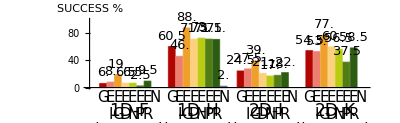

```mathematica
selectedData=selectData[sortedData,{"ID"->{"1D","2D"}}];
selectedData=removeData[selectedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}]; (* Removed 2D-J *)
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-1.2,-8}]};
padding={{40,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"1D-F"},{"(0,1,0,1)"}}],Grid[{{"1D-H"},{"(0,0,1,1)"}}],Grid[{{"2D-I"},{"(0,0,1,1)"}}],Grid[{{"2D-K"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_1d_2d.eps",%];
```

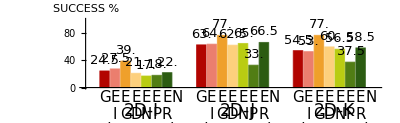

```mathematica
selectedData=selectData[sortedData,{"ID"->{"2D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"2D-I"},{"(0,0,1,1)"}}],Grid[{{"2D-J"},{"(0,0,1,1)"}}],Grid[{{"2D-K"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
```

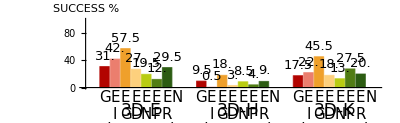

```mathematica
selectedData=selectData[sortedData,{"ID"->{"3D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"3D-E"},{"(0,0,1,2)"}}],Grid[{{"3D-H"},{"(0,0,1,1)"}}],Grid[{{"3D-K"},{"(0,0,0,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_3d.eps",%];
```

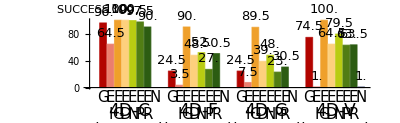

```mathematica
selectedData=selectData[sortedData,{"ID"->{"4D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-1.2,-8}]};
padding={{40,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"4D-C"},{"(0,0,1,1)"}}],Grid[{{"4D-F"},{"(0,1,0,1)"}}],Grid[{{"4D-G"},{"(0,1,0,1)"}}],Grid[{{"4D-V"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_4d.eps",%];
```

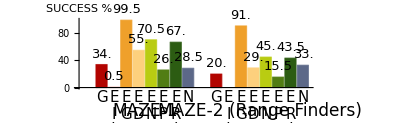

```mathematica
selectedData=selectData[sortedData,{"ID"->{"MAZE"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.0,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"MAZE-1"},{"(0,1,1,0)"}}],Grid[{{"MAZE-2 (Range Finders)"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_maze.eps",%];
```

## Hyper Experiments All Comparison [TEMPLATE]

```mathematica
names={"HNEAT_GECCO","HGP","HGP_GPEFS_NOGENERAL_GECCO","HGP_GPEFS_GENERAL_BEST_GECCO","ROBO_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G",""}->{"T",""},{"G",x:_}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T",""}->{"G",""}}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GP.DISTANCE","RECO.GENERATOR","PROBLEM"}];
```

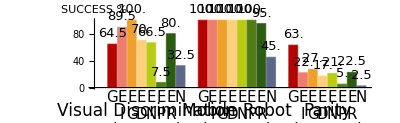

```mathematica
selectedData=selectData[sortedData,{"ID"->{"XOR","FC","ROBO"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"Visual Discrimination"},{"(0,0,0,2)"}}],Grid[{{"Mobile Robot"},{"(0,1,0,1)"}}],Grid[{{"Parity"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_fc_robo_xor.eps",%];
```

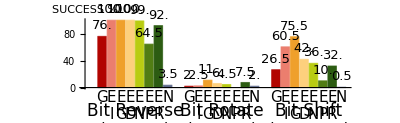

```mathematica
selectedData=selectData[sortedData,{"ID"->{"RECO1D"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"Bit Reverse"},{"(0,0,0,2)"}}],Grid[{{"Bit Rotate"},{"(1,0,0,1)"}}],Grid[{{"Bit Shift"},{"(0,0,0,10)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_reco.eps",%];
```

## Hyper Initial EXPS

```mathematica
names={"HAT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
padding={{30,0},{80,25}};
sortedData = sortDataByParams[data,{"SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
solverRewrite,
functionImplRewrite
}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT"}]
```

ID | PARAM FILE | SOLVER | ID | GPAT.DISTANCE | GPAT.FUNCTION_IMPL | RECO.GENERATOR | PROBLEM | GPAT.DISTANCE_CACT
{AT,N} | HAT_R/parameters_001.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctions$ | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO | 0.
{AT,NC} | HAT_R/parameters_002.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsNoConsts$ | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO | 0.
{AT,GP} | HAT_R/parameters_003.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsLikeGP$ | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | RECO | 0.
{AT,N} | HAT_R/parameters_004.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctions$ | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO | 0.
{AT,NC} | HAT_R/parameters_005.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsNoConsts$ | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO | 0.
{AT,GP} | HAT_R/parameters_006.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsLikeGP$ | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | RECO | 0.
{AT,N} | HAT_R/parameters_007.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctions$ | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO | 0.
{AT,NC} | HAT_R/parameters_008.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsNoConsts$ | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO | 0.
{AT,GP} | HAT_R/parameters_009.txt | GPAT | RECO1D | RANDOM | gpat.ATFunctionsLikeGP$ | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | RECO | 0.
{AT,N} | HAT_R/parameters_010.txt | GPAT | FC | RANDOM | gpat.ATFunctions$ |  | FIND_CLUSTER | 0.
{AT,NC} | HAT_R/parameters_011.txt | GPAT | FC | RANDOM | gpat.ATFunctionsNoConsts$ |  | FIND_CLUSTER | 0.
{AT,GP} | HAT_R/parameters_012.txt | GPAT | FC | RANDOM | gpat.ATFunctionsLikeGP$ |  | FIND_CLUSTER | 0.
{AT,N} | HAT_R/parameters_013.txt | GPAT | XOR | RANDOM | gpat.ATFunctions$ | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR | 0.
{AT,NC} | HAT_R/parameters_014.txt | GPAT | XOR | RANDOM | gpat.ATFunctionsNoConsts$ | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR | 0.
{AT,GP} | HAT_R/parameters_015.txt | GPAT | XOR | RANDOM | gpat.ATFunctionsLikeGP$ | hyper.experiments.reco.problem.PatternGeneratorXOR | XOR | 0.

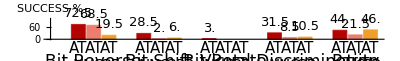

```mathematica
selectedData=selectData[sortedData,{"ID"->{"FC"}}];
plotBooleanAsBarChartPub[sortedData,"SUCCESS",listOfIndirectProblems,0.0,3,PlotRange->plotRange, ImagePadding->padding,AspectRatio->0.25/GoldenRatio]
```

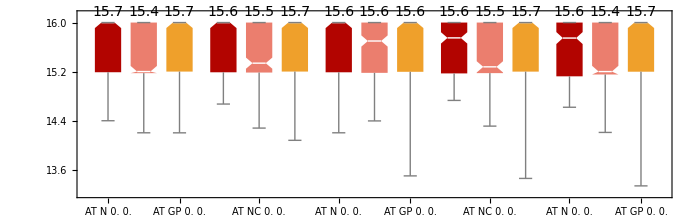
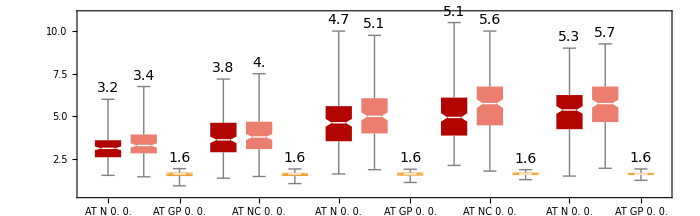
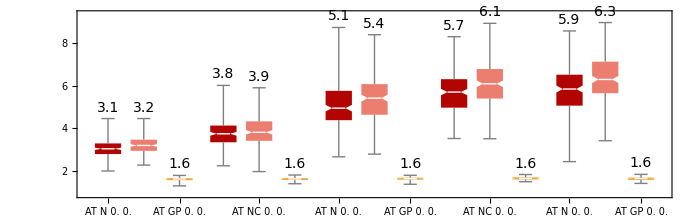
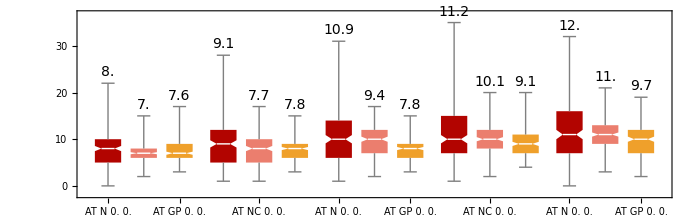
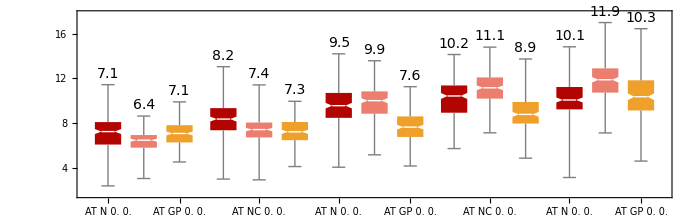
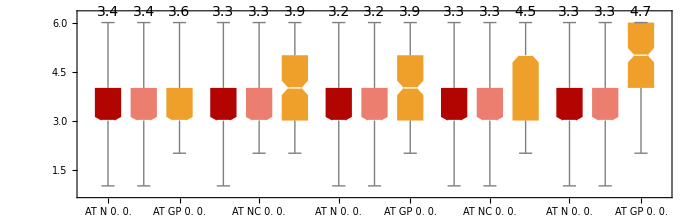
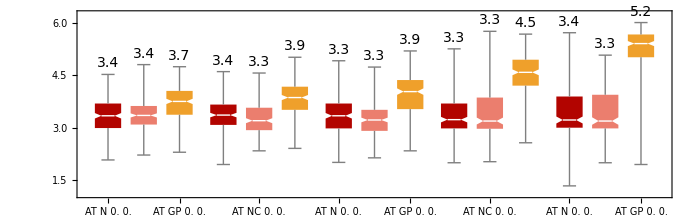
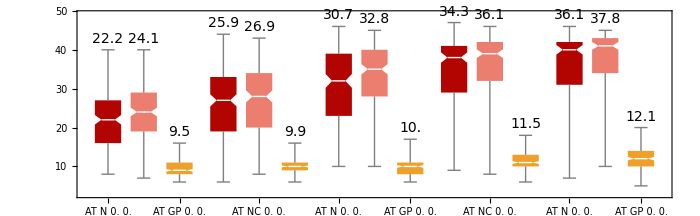
{BSF
-Graphics-,ARITY_BSF
-Graphics-,ARITY_LG
-Graphics-,CONSTANTS_BSF
-Graphics-,CONSTANTS_LG
-Graphics-,DEPTH_BSF
-Graphics-,DEPTH_LG
-Graphics-,LEAVES_BSF
-Graphics-,LEAVES_LG
-Graphics-,NODES_BSF
-Graphics-,NODES_LG
-Graphics-}

```mathematica
selectedData=selectData[sortedData,{"ID"->{"XOR"}}];
Grid[{{Style[#,FontSize->17]},
{plotAsBoxWhiskerChartPub[selectedData,#,{"Bit Reverse","Bit Rotate","Bit Shift"},0.0,3,PlotRange->All,PlotRangePadding->{Automatic,Automatic}]}}]&/@{"BSF","ARITY_BSF","ARITY_LG","CONSTANTS_BSF","CONSTANTS_LG","DEPTH_BSF","DEPTH_LG" ,"LEAVES_BSF","LEAVES_LG","NODES_BSF","NODES_LG"}
```

## VIVAE BSF

```mathematica
Needs["PlotLegends`"]
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
enlarge[list_,bsfAvg_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvgGP = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_GP_GECCO"}]);
bsfAvgBASIC = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_BASIC_GECCO"}]);
bsfAvgGENERAL = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_GENERAL_GECCO"}]);
bsfAvgISO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_ISO_GECCO"}]);
bsfAvgNODES = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_NODES_GECCO"}]);
bsfAvgPHENO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_PHENO_GECCO"}]);
bsfAvgRANDOM = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_RANDOM_GECCO"}]);
bsfAvgNEAT = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HNEAT_robo_NEAT_GECCO"}]);
```

```mathematica
maxGenerations=Max@@(Max[Length[#]&/@#]&/@{bsfAvgGP,bsfAvgBASIC,bsfAvgGENERAL,bsfAvgISO,bsfAvgNODES,bsfAvgPHENO,bsfAvgRANDOM,bsfAvgNEAT})
```

50

```mathematica
bsfAvgGP=Mean[(enlarge/@bsfAvgGP)];
bsfAvgBASIC=Mean[(enlarge/@bsfAvgBASIC)];
bsfAvgGENERAL=Mean[(enlarge/@bsfAvgGENERAL)];
bsfAvgISO=Mean[(enlarge/@bsfAvgISO)];
bsfAvgNODES=Mean[(enlarge/@bsfAvgNODES)];
bsfAvgPHENO=Mean[(enlarge/@bsfAvgPHENO)];
bsfAvgRANDOM=Mean[(enlarge/@bsfAvgRANDOM)];
bsfAvgNEAT=Mean[(enlarge/@bsfAvgNEAT)];
```

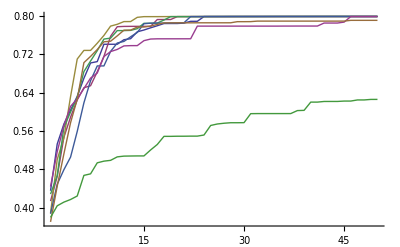

```mathematica
ListLinePlot[{bsfAvgGP,bsfAvgBASIC,bsfAvgGENERAL,bsfAvgISO,bsfAvgNODES,bsfAvgPHENO,bsfAvgRANDOM,bsfAvgNEAT}, PlotRange->All]
```

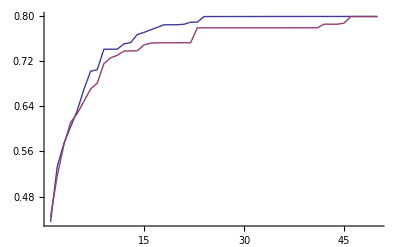

```mathematica
ListLinePlot[{bsfAvgGP,bsfAvgPHENO}, PlotRange->All]
```